```mathematica
ClearAll["Global`*"];
```

```mathematica
dat=ReadList["kerr.dat",{Number,Number,Number,Number,Number,Number}];
nx=251;ny=30;
xmax=dat[[251,1]];xmin=dat[[1,1]];
ymax=dat[[nx*ny,2]];ymin=dat[[1,2]];
rh=0.0662902;OmegaH=1.11118;
```

```mathematica
cts =NSolve[OmegaH==Sqrt[x(x-rh)]/((rh-x)(rh-2x)),x];
ct=cts[[2,1,2]];
```

```mathematica
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2/M
a/M
RH = M+Sqrt[M^2-a^2];
```

0.415392

0.414068

0.996812

```mathematica
Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2],1000]
```

```mathematica
f1[r_,θ_]:=(1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2;
f2=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,4]]]},{i,1,ny},{j,1,nx}];
f0=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,5]]]},{i,1,ny},{j,1,nx}];
W=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,6]]},{i,1,ny},{j,1,nx}];
H[r_]:=1-rh/r;
```

```mathematica
(*if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];*)
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
```

```mathematica
(*f1 = if1;*)
f2=if2;
f0=if0;
W=iW;
```

```mathematica
f1[10,0]
f2[10,0]
f0[10,0]
W[10,0]
```

1.07963

1.07962

0.926249

0.000306394

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=-f2[r,θ]*r^2*Sin[θ]^2W[r,θ];

metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_] := R - a^2/RH;
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coords[[k]]]+D[metric[[s,k]],coords[[j]]]-D[metric[[j,k]],coords[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.05*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler 
I want to plot in the R, i.e. BL, radial coordinates, so for solution 1, I have to translate to R via r = R - a^2/RH *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/RH) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/RH) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/RH) Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
rh
ct
M
a
```

0.0662902

-0.382247

0.415392

0.414068

```mathematica
τend=.;uinvar = 0;
τPlot=100;
AbsoluteTiming[soln=computeSoln[τPlot,{-0.1,0,0.0075},{0,Rtor[8 RH],π/2,0}]][[1]]
```

0.1835

```mathematica
xyzsoln=sphslnToCartsln[soln];
Table[{τi,coords[[2]][τ] /. soln /. τ -> τi},{τi,0,τend,1}];
horizpl=PolarPlot[RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
```

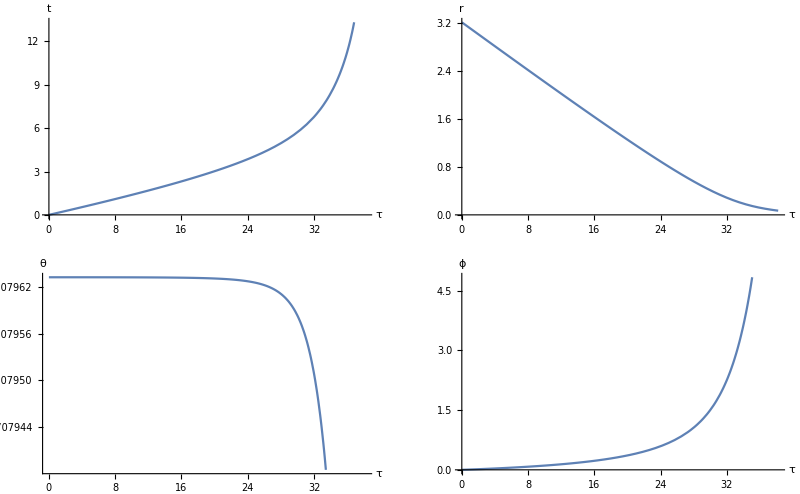

```mathematica
GraphicsGrid[{{Plot[{Evaluate[coords[[1]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","t"}],Plot[{Evaluate[coords[[2]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[{Evaluate[coords[[3]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[{Evaluate[coords[[4]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
```

For initial coordinates={0,3.20605,π/2,0} and initial velocities={-0.1,0,0.0075} the particle crosses the horizon at τend=38.1784

With final coordinates={t = 22.4236,r = 0.0696047,θ = 1.57078,ϕ = 18.0079}

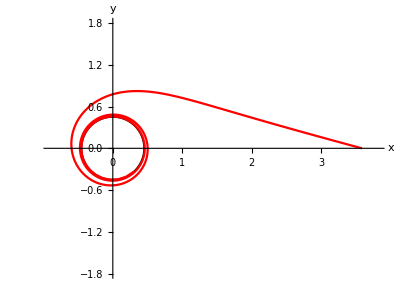

```mathematica
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot[τPlot,{0,Rtor[8 RH],π/2,0},{-0.1,0,0.0075},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2 RH,8.5 RH},{-4 RH,4 RH}}]
```

```mathematica
(* other coords *)
Print["a=",a,", M=",M,", rh=",rh,", ct=",ct]
r0 = 50;
NumberForm[tt/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[rr/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[θθ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[ϕϕ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[tϕ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[christoffel[[1,1,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[2,2,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[1,1,1]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[3,2,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
```

a=0.414068, M=0.415392, rh=0.0662902, ct=-0.382247

0.0001714001482532328

-0.0001701721465744605

0.

-6.84369934714486×10^-14

```mathematica
τend
```

32.253

```mathematica
Clear[soln]
```

The particle did not cross the horizon for initial coordinates={0,4.10313,π/2,0} and initial velocities={-0.1,0,0.0055}

With final coordinates={t = 66.7513,r = 44.8952,θ = 1.5708,ϕ = 12.5768}

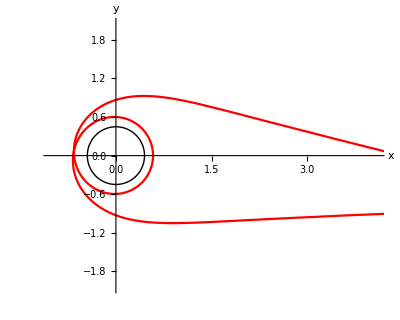

numerical.dat

```mathematica
τend=.;uinvar=0;
τPlot=500;
initialR=Rtor[10 RH];
(*soln=computeSoln[τPlot,{-0.1,0,0.0075},{0,Rtor[50 RH],π/2,0}];*)
genXYPlot[τPlot,{0,initialR,π/2,0},{-0.1,0,0.0055},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange->{{-initialR/4,initialR},{-initialR/2,initialR/2}}]
Export["numerical.dat",Table[{τi,NumberForm[coords[[2]][τ]/.soln/.τ->τi,16][[1]],NumberForm[coords[[3]][τ]/.soln/.τ->τi,16][[1]],NumberForm[coords[[4]][τ]/.soln/.τ->τi,16][[1]]},{τi,0,τend,1}]]
```